Name: Karan Sharma 
College Roll No.: 2232191
University Roll No.: 22036563079
Course: BSc. (Hons.) Mathematics/Year 3/Complex Analysis 
Section: A

## Practical 11: Contour Integration

Question : Perform the following Line integrals. 
1 : Perform the contour integration  C z dz 
	where C is the portion of the parabola x = y2 + 2 y joining - 1 - ⅈ to 3 + ⅈ.

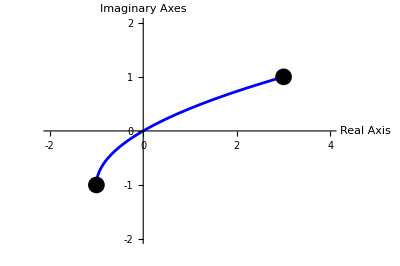

The Value of the contour integration  C zⅆz is  -1 1 f[z[t]]z'[t]ⅆt = 4+2 ⅈ

where C: z[t] = (2+ⅈ) t+t^2, for -1 ≤ t ≤ 1

```mathematica
ClearAll;
f[z_] = z; 
z[t_] = (t^2 + 2 t) + ⅈ t; 
val = Integrate[ f[z[t]] * z '[t], {t,-1,1}];
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}];

g1 = ParametricPlot[V[t], {t, -1, 1}, PlotRange -> {{-2, 4}, {-2, 2}}, 
Ticks -> {Range[-2, 4, 1], Range[-2, 2, 1]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue];

g2 = Graphics[{PointSize[0.03], Point[{-1, -1}], Point[{3, 1}]}]; 
Show[g1, g2] 
Print["The Value of the contour integration ", " C ", f[z], "ⅆz is ", " -1 1 ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for -1 ≤ t ≤ 1"];
```

2 : Perform the contour integration  C z2 - 2 z + 1 dz 
	where C is the contour given by x = y2 + 1 where - 2 ≤ y ≤ 2.

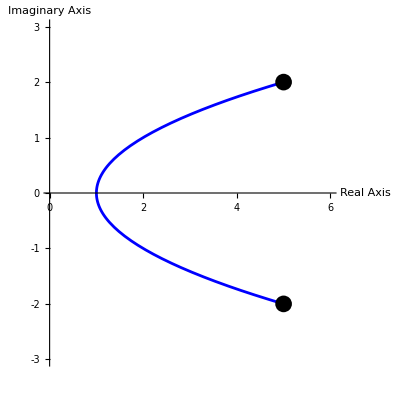

The Value of the contour integration  C 1+2 z+z^2 ⅆz is  -2 2 f[z[t]]z'[t]ⅆt = (416 ⅈ)/3

where C: z[t] = 1+ⅈ t+t^2, for -2 ≤ t ≤ 2

```mathematica
f[z_] = z^2 + 2* z + 1; 
z[t_] = (t^2 + 1) + ⅈ t; 
val = Integrate[ f[z[t]] * z'[t],{t,-2,2}];
V[t_] = ComplexExpand[{Re[z[t]], Im[z[t]]}]; 

g1 = ParametricPlot[V[t], {t, -2, 2}, PlotRange -> {{0, 6}, {-3, 3}}, 
Ticks -> {Range[0, 6, 1], Range[-3, 3, 1]}, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotStyle -> Blue];

g2 = Graphics[{PointSize[0.03], Point[{5, -2}], Point[{5, 2}]}]; Show[g1, g2]

Print["The Value of the contour integration ", " C ", f[z], " ⅆz is ", " -2 2 ", "f[z[t]]z'[t]", "ⅆt ", "= ", val]; 
Print["where C: z[t] = ", z[t], ", for -2 ≤ t ≤ 2"];
```

3 : Show that  C1 z dz =  C2 z dz 
	where C1 is the line segment from - 1 - ⅈ to 3 + ⅈ and 
    		C2 is the portion of the parabola x = y2 + 2 y joining - 1 - ⅈ to 3 + ⅈ . 
   Also plot the contours C1 and C2 .

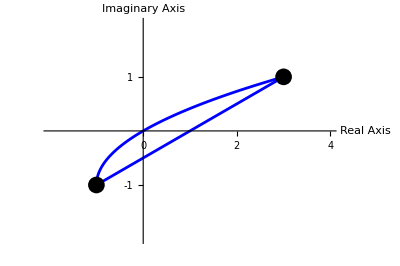

```mathematica
ClearAll;
f[z_] = z; 
z0 = -1 - ⅈ; 
z1 = 3 + ⅈ; 
x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1]; 
c1[t_] = x0 + (x1 - x0) t + ⅈ(y0 + (y1 - y0) t); 
c2[t_] = (t^2 + 2 t) + ⅈ t; 

Int1 = Integrate[f[c1[t]] *(c1'[t]), {t,0,1}]; 
Int2 = Integrate[f[c2[t]] * (c2'[t]), {t, -1,1}];

V1[t_] = ComplexExpand[{Re[c1[t]], Im[c1[t]]}];
V2[t_] = ComplexExpand[{Re[c2[t]], Im[c2[t]]}]; 

g1 = ParametricPlot[V1[t], {t, 0, 1}, PlotRange -> {{-2, 4}, {-2, 2}}, Ticks -> {Range[0, 6, 1], Range[-3, 3, 1]}, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotStyle -> Blue]; g2 = ParametricPlot[V2[t], {t, -1, 1}, PlotRange -> {{-2, 4}, {-2, 2}}, Ticks -> {Range[0, 6, 1], Range[-3, 3, 1]}, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotStyle -> Blue];
g3 = Graphics[{PointSize[0.03], Point[{x0, y0}], Point[{x1, y1}]}]; 
Show[g1, g2, g3]
```

```mathematica
If[Int1== Int2, 
Print["The integrals  C1 z dz and  C2 z dz are equal and equal to ", Int1, "." ],Print["Integrals are not equal."]]
```

The integrals  C1 z dz and  C2 z dz are equal and equal to 4+2 ⅈ.